```mathematica
SetDirectory["G:\\My Drive\\Projects\\FourierDisplay\\Software"];
LoadPack:=Get["G:\\My Drive\\Projects\\FourierDisplay\\Software\\FourierPack.wl"];
(*Remove/@Names["FourierPack`*"];*)
LoadPack;
```

## LoadImageTours

```mathematica
baseDir = "G:\\My Drive\\Projects\\FourierDisplay\\Software\\Resources\\HandwritingImages\\";
imageDirs = baseDir<>#&/@{"Renkert.jpg", "Phil.jpg","JohnHancock.png"};
images = Import/@imageDirs;
```

```mathematica
processedImages = (ImageResize[ImageAdjust[#,{1,.5}],1000])&/@images;
processedImages = MapAt[ImageRotate,processedImages, {{1},{2}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
points = ImageLinePoints/@processedImages;
pointsTour = MakeTour/@points;
```

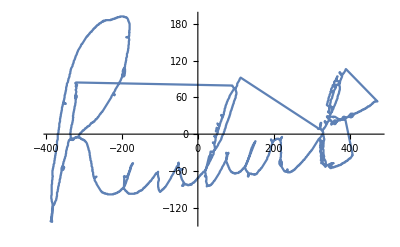
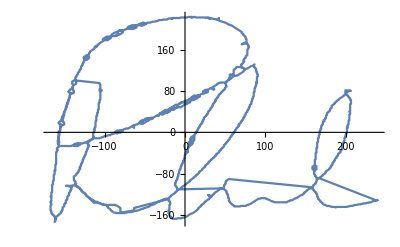
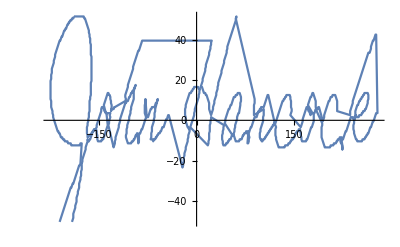

```mathematica
ListLinePlot/@pointsTour
```

## Circles

```mathematica
samples = UniformResample[PrependIndices[#,"ParametrizationType"->"EuclidianDistance"],500,"ParametrizationType"->"Linear"]&/@pointsTour;
```

```mathematica
coefObjects = CnFFT[MakeComplex[#["SamplePoints"]], 200]&/@samples; (*Takes 50 circles by largest radius*)
```

```mathematica
circleObjects = MapThread[ApproxFunction[#2["CoefficientFunction"],t,Length@#1["SamplePoints"],#2["CoefficientList"], "Sort"->False]&,{samples, coefObjects}];
```

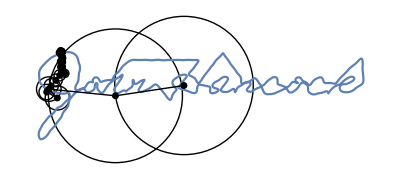

```mathematica
With[{circle = 3},EpicyclePlot[circleObjects[[circle]], {t,0,samples[[circle]]["Length"]}]]
```

## Spinners

```mathematica
Manipulate[SpinnerRow[circleObjects[[1]],t, "NumSpinners"->10, "StatViewer"->False],{t,0,samples[[1]]["Length"]}]
```

## Combined Plot

```mathematica
Head@circleObjects[[1]]
```

Association

```mathematica
Keys[circleObjects[[3]]]
```

{Coefficients,Radii,Speeds,Terms,ArmEnds,Centers,Function}

```mathematica
With[{circle = 3},Manipulate[EpicyclePlot[circleObjects[[circle]],{t,0,$T,samples[[circle]]["Length"]},"Spinners"->True, "NumSpinners"->10, "PlotRange"->"Plot"],{$T,0,samples[[circle]]["Length"]}]]
```

```mathematica
(*With[{circle = 3},EpicyclePlot[circleObjects[[circle]],{t,0,samples[[circle]]["Length"]},"Spinners"->True, "NumSpinners"->10, "PlotRange"->With[{pnts=samples[[circle]]["SamplePoints"]},{{Min@#,Max@#}&@(First/@pnts),{Min@#,Max@#}&@(Last/@pnts)}], "Movie"->True]]*)
```